# Motion in an Electric Field

### For a particle in an electric field, the Lagrangian is:

```mathematica
L=m/(2n)(-t'[T]^2+x'[T]^2)-(m n)/2+(k t'[T]x[T])
```

-(m n)/2+k x[T] t'[T]+(m (-t'[T]^2+x'[T]^2))/(2 n)

### Let’s test all the derivatives and see if we get the right results:

#### Partials wrt x

```mathematica
D[L,x[T]]
D[L,x'[T]]
```

k t'[T]

(m x'[T])/n

```mathematica
D[D[L,x'[T]],T]
```

(m x''[T])/n

#### Partials wrt t

```mathematica
D[L,t[T]]
D[L,t'[T]]
```

0

k x[T]-(m t'[T])/n

```mathematica
D[D[L,t'[T]],T]
```

k x'[T]-(m t''[T])/n

Yes we do!

### Find the equations of motion:

```mathematica
D[D[L,x'[T]],T]-D[L,x[T]]==0
```

-k t'[T]+(m x''[T])/n==0

```mathematica
D[D[L,t'[T]],T]-D[L,t[T]]==0
```

k x'[T]-(m t''[T])/n==0

```mathematica
D[D[D[L,t'[T]],T]-D[L,t[T]],T]==0
```

k x''[T]-(m t^(3)[T])/n==0

NOT SURE WHY WE DID THIS ?? ^

### Solve the equation of motion to get x(T) and t(T):

```mathematica
soltx=DSolve[{- k t'[T]+(m x''[T])/n==0,k x'[T]-(m t''[T])/n==0, x[0]==xa,x[1]==xb,t[0]==ta,t[1]==tb},{t,x},T]
```

{{t→Function[{T},-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)],x→Function[{T},-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb)]}}

```mathematica
Factor[FullSimplify[t[T]/.soltx[[1]]/.{xa->0,ta->0},Trig->True]] (* Simplify the t solution *)
```

Csch[(k n)/(2 m)] (tb Cosh[(k n (-1+T))/(2 m)]+xb Sinh[(k n (-1+T))/(2 m)]) Sinh[(k n T)/(2 m)]

```mathematica
Factor[FullSimplify[x[T]/.soltx[[1]]/.{xa->0,ta->0},Trig->True]] (* Simplify the x solution *)
```

Csch[(k n)/(2 m)] (xb Cosh[(k n (-1+T))/(2 m)]+tb Sinh[(k n (-1+T))/(2 m)]) Sinh[(k n T)/(2 m)]

#### Trajectory Plots:

```mathematica
Clear[xa,xb,ta, tb,m, k, n];
```

```mathematica
par={xa->0,xb->4,ta-> 0, tb -> 6,m->1,n->1, k->2};
par2={xa->0,xb->4,ta-> 0, tb -> 6,m->1,n->1, k->3};(* Different parameters *)
```

#### Simplified expressions for t :

```mathematica
f=t[T]/.soltx⟦1⟧/.par
f2=t[T]/.soltx⟦1⟧/.par2
```

-(ⅇ^(-2 T) (2 ⅇ^2+10 ⅇ^(2 T)-10 ⅇ^(4 T)-2 ⅇ^(2+2 T)))/(2 (-1+ⅇ^2))

-(ⅇ^(-3 T) (2 ⅇ^3+10 ⅇ^(3 T)-10 ⅇ^(6 T)-2 ⅇ^(3+3 T)))/(2 (-1+ⅇ^3))

#### Simplified expressions for x :

```mathematica
g=x[T]/.soltx⟦1⟧/.par
g2=x[T]/.soltx⟦1⟧/.par2
```

-(ⅇ^(-2 T) (-2 ⅇ^2+10 ⅇ^(2 T)-10 ⅇ^(4 T)+2 ⅇ^(2+2 T)))/(2 (-1+ⅇ^2))

-(ⅇ^(-3 T) (-2 ⅇ^3+10 ⅇ^(3 T)-10 ⅇ^(6 T)+2 ⅇ^(3+3 T)))/(2 (-1+ⅇ^3))

#### Plots of x and t wrt to T :

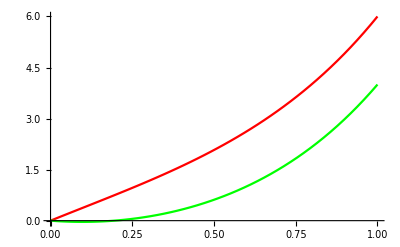

```mathematica
Plot[{f,g},{T,0,1},PlotStyle->{Red,Green}]
```

#### Trajectory for particle in electric field (t versus x) :

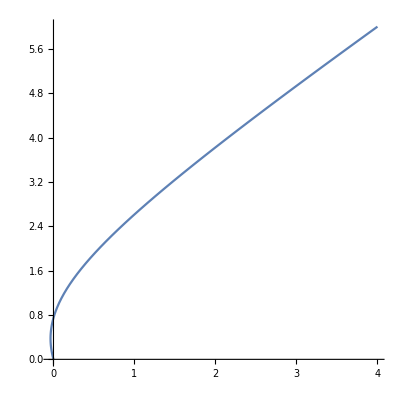

```mathematica
ParametricPlot[{g,f},{T,0,1},AspectRatio->1]
```

#### Attempt at Manipulate function:

```mathematica
(* Variables storing expressions for x and t *)
xm= x[T]/.soltx⟦1⟧
```

-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb)

```mathematica
tm=t[T]/.soltx⟦1⟧
```

-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)

```mathematica
Manipulate[ ParametricPlot[{-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb),-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)},{T,0,1},AspectRatio->1],{xa,0,100},{xb,0,100},{ta,0,100},{tb,0,100},{m,0.0001,100},{n,0.0001,100},{k,0.0001,100}]
```

### Find the classical action:

```mathematica
LL =Simplify[L/.soltx[[1]]] (* Storing the Lagrangian with the solution plugged in *)
```

1/(4 (-1+ⅇ^((k n)/m))^2 m)ⅇ^(-(2 k n T)/m) n (-2 ⅇ^((2 k n T)/m) m^2-2 ⅇ^((2 k n (1+T))/m) m^2+4 ⅇ^((k n (1+2 T))/m) m^2+ⅇ^((4 k n T)/m) k^2 (ta-tb+xa-xb)^2+ⅇ^((2 k n)/m) k^2 (ta-tb-xa+xb)^2-ⅇ^((k n (1+3 T))/m) k^2 (ta^2-2 ta tb+tb^2+2 ta xa-2 tb xa+xa^2-xb^2)-ⅇ^((k n (1+T))/m) k^2 (ta^2+tb^2+2 tb xa+xa^2-2 ta (tb+xa)-xb^2)-ⅇ^((k n (2+T))/m) k^2 (ta^2-2 ta tb+tb^2-xa^2+2 ta xb-2 tb xb+xb^2)-ⅇ^((3 k n T)/m) k^2 (ta^2+tb^2-xa^2+2 tb xb+xb^2-2 ta (tb+xb)))

```mathematica
Scl=Simplify[Integrate[LL,{T,0,1}]] (* Integrating the Lagrangian over T to get the classical action *)
```

1/4 (-2 (m n+k (ta-tb) (xa+xb))-k (ta-tb+xa-xb) (ta-tb-xa+xb) Coth[(k n)/(2 m)])

```mathematica
Scl/.{xa->0,ta->0} (* Using simplified initial values for x and t *)
```

1/4 (-2 (m n-k tb xb)-k (-tb-xb) (-tb+xb) Coth[(k n)/(2 m)])